```mathematica
f[x_, xmin_,xmax_] = -((2*x-xmin-xmax)/(xmax-xmin))^3;
g[x_,y_,xmin_,xmax_,ymin_,ymax_] = {
f[x, xmin, xmax] * Sqrt[1 - f[y,ymin,ymax]^2/2],
f[y, ymin, ymax] * Sqrt[1 - f[x,xmin,xmax]^2/2]
};
```

```mathematica
Norm[g[20,7,-20,20,-10,10]]
```

1

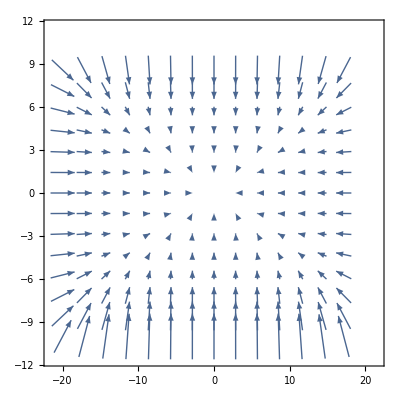

```mathematica
VectorPlot[g[x,y,-20,20,-10,10],{x,-20,20},{y,-10,10}]
```